# h=A+B+A^-1+B^-1(case 2)

Computation of the sequences η := (|| h_n((||)_2)^2), ξ:=(ξ_n) , ρ:=(η_n),  ζ:=(ζ_n), m:=(m_n) , tables, graphs, and densities for the paper
“A COMPUTATIONAL APPROACH TO THE THOMPSON GROUP F” 
by S. Haagerup, U. Haagerup, M. Ramirez-Solano:

```mathematica
ηhalf={2,6,18,54,172,538,1750,5662,19354,67640,248808,955226,3873742,16469058,72875074,335047398,1582466740,7674516890,37775752458,189434653576,959151943910,4922901950252,25435065012668,132837576943418}
idsNotreduced={0,0,0,0,0,0,0,0,0,20,0,124,0,528,0,2168,0,9376,0,42340,0,191584,0,884020}
```

{2,6,18,54,172,538,1750,5662,19354,67640,248808,955226,3873742,16469058,72875074,335047398,1582466740,7674516890,37775752458,189434653576,959151943910,4922901950252,25435065012668,132837576943418}

{0,0,0,0,0,0,0,0,0,20,0,124,0,528,0,2168,0,9376,0,42340,0,191584,0,884020}

```mathematica
Clear[ids]
ids[-1]=0;
ids[0]=0;
idsList=Table[ids[n]=idsNotreduced⟦n⟧-3ids[n-2],{n,1,Length[idsNotreduced]}];
η=2 ηhalf-idsList^2
Clear[ids,idsList]
```

{4,12,36,108,344,1076,3500,11324,38708,134880,497616,1906356,7747484,32825220,145750148,668749196,3164933480,15314270964,75551504916,378261586048,1918303887820,9831967554120,50870130025336,265393048436340}

```mathematica
η
```

{4,12,36,108,344,1076,3500,11324,38708,134880,497616,1906356,7747484,32825220,145750148,668749196,3164933480,15314270964,75551504916,378261586048,1918303887820,9831967554120,50870130025336,265393048436340}

```mathematica
q=4-1;
ξ=η-(q+1)Table[q^(n-1),{n,1,Length[η]}]
ρ=ξ-(q-1)Table[Total[ξ⟦Range[n-1]⟧],{n,1,Length[ξ]}]
ζ=ρ-(q-1)Table[Total[ρ⟦Range[n-1]⟧],{n,1,Length[ξ]}]
m=Table[Binomial[2n,n] q^n+Total[Table[Binomial[2n,n-k] q^(n-k)(ζ⟦k⟧+1-q),{k,1,n}]],{n,1,Length[ζ]}]
mq=Table[Binomial[2n,n] q^n+Total[Table[Binomial[2n,n-k] q^(n-k)(1-q),{k,1,n}]],{n,1,Length[ζ]}]
Ntuple=Length[m]
```

{0,0,0,0,20,104,584,2576,12464,56148,261420,1197768,5621720,26447928,126618272,611353568,2992746596,14797710312,74001822960,373612540180,1904356750216,9790126141308,50744605786900,265016475721032}

{0,0,0,0,20,64,336,1160,5896,24652,117628,531136,2559552,12142320,59416808,290915560,1449601452,7269071976,36877764000,188484835300,972003964976,5049059855636,26423287218612,139205945578944}

{0,0,0,0,20,24,168,320,2736,9700,53372,231624,1197768,5661432,28651280,141316416,718171188,3638438808,18708986880,96560530180,503109989256,2636157949964,13912265601668,73848349524776}

{4,28,232,2092,19884,196096,1988452,20612364,217561120,2331456068,25311956784,277937245744,3082543843552,34493827011868,389093033592912,4420986174041164,50566377945667804,581894842848487960,6733830314028209908,78331435477025276852,915607264080561034564,10750847942401254987096,126768974481834814357308,1500753741925909645997904}

{4,28,232,2092,19864,195352,1970896,20275660,211823800,2240795848,23951289520,258255469816,2805534253552,30675477376432,337306474674592,3727578443380492,41376874025687032,461121792658583272,5157384457905440752,57869888433073055272,651266142688270063312,7349148747954997832272,83136542574028253115232,942624010510370287581112}

24

```mathematica
Grid[Transpose[{Range[Length[η]],η,ξ,ρ,ζ,m}],Alignment->Left]
```

1 | 4 | 0 | 0 | 0 | 4
2 | 12 | 0 | 0 | 0 | 28
3 | 36 | 0 | 0 | 0 | 232
4 | 108 | 0 | 0 | 0 | 2092
5 | 344 | 20 | 20 | 20 | 19884
6 | 1076 | 104 | 64 | 24 | 196096
7 | 3500 | 584 | 336 | 168 | 1988452
8 | 11324 | 2576 | 1160 | 320 | 20612364
9 | 38708 | 12464 | 5896 | 2736 | 217561120
10 | 134880 | 56148 | 24652 | 9700 | 2331456068
11 | 497616 | 261420 | 117628 | 53372 | 25311956784
12 | 1906356 | 1197768 | 531136 | 231624 | 277937245744
13 | 7747484 | 5621720 | 2559552 | 1197768 | 3082543843552
14 | 32825220 | 26447928 | 12142320 | 5661432 | 34493827011868
15 | 145750148 | 126618272 | 59416808 | 28651280 | 389093033592912
16 | 668749196 | 611353568 | 290915560 | 141316416 | 4420986174041164
17 | 3164933480 | 2992746596 | 1449601452 | 718171188 | 50566377945667804
18 | 15314270964 | 14797710312 | 7269071976 | 3638438808 | 581894842848487960
19 | 75551504916 | 74001822960 | 36877764000 | 18708986880 | 6733830314028209908
20 | 378261586048 | 373612540180 | 188484835300 | 96560530180 | 78331435477025276852
21 | 1918303887820 | 1904356750216 | 972003964976 | 503109989256 | 915607264080561034564
22 | 9831967554120 | 9790126141308 | 5049059855636 | 2636157949964 | 10750847942401254987096
23 | 50870130025336 | 50744605786900 | 26423287218612 | 13912265601668 | 126768974481834814357308
24 | 265393048436340 | 265016475721032 | 139205945578944 | 73848349524776 | 1500753741925909645997904

```mathematica
μ=Function[d,If[d==1,1,Module[{k,factores,exponentes,isProductOfDistinctPrimes},
{factores,exponentes}=Transpose[FactorInteger[d]];
k=Length[factores];
If[Max[exponentes]==1 ,isProductOfDistinctPrimes=1,isProductOfDistinctPrimes=0];
If[isProductOfDistinctPrimes==1, (-1)^k,0]
]]]
ζpFunction=Function[n,Module[{divisors,i},
divisors=Divisors[n];
Total[Table[μ[n/divisors⟦i⟧]ζ[[divisors⟦i⟧]],{i,1,Length[divisors]}]]
]]
```

Function[d,If[d==1,1,Module[{k,factores,exponentes,isProductOfDistinctPrimes},{factores,exponentes}=Transpose[FactorInteger[d]];k=Length[factores];If[Max[exponentes]==1,isProductOfDistinctPrimes=1,isProductOfDistinctPrimes=0];If[isProductOfDistinctPrimes==1,(-1)^k,0]]]]

Function[n,Module[{divisors,i},divisors=Divisors[n];Total[Table[μ[n/divisors⟦i⟧] ζ⟦divisors⟦i⟧⟧,{i,1,Length[divisors]}]]]]

```mathematica
Table[{n,ζpFunction[n]},{n,1,24}]//ColumnForm
```

{1,0}
{2,0}
{3,0}
{4,0}
{5,20}
{6,24}
{7,168}
{8,320}
{9,2736}
{10,9680}
{11,53372}
{12,231600}
{13,1197768}
{14,5661264}
{15,28651260}
{16,141316096}
{17,718171188}
{18,3638436048}
{19,18708986880}
{20,96560520480}
{21,503109989088}
{22,2636157896592}
{23,13912265601668}
{24,73848349292832}

```mathematica
Table[{n,ζpFunction[n]/(2n)},{n,1,24}]//ColumnForm
```

{1,0}
{2,0}
{3,0}
{4,0}
{5,2}
{6,2}
{7,12}
{8,20}
{9,152}
{10,484}
{11,2426}
{12,9650}
{13,46068}
{14,202188}
{15,955042}
{16,4416128}
{17,21122682}
{18,101067668}
{19,492341760}
{20,2414013012}
{21,11978809264}
{22,59912679468}
{23,302440556558}
{24,1538507276934}

```mathematica
mm=Riffle[0Range[Length[m]],m]
Table[d[n]=Det[Table[If[i+j==0,1,mm⟦i+j⟧],{i,0,n},{j,0,n}]],{n,0,Length[m]}]
d[-1]=1;
Table[k[n]=(d[n-1]/d[n])^(1/2),{n,0,Length[m]}]
Table[α[n]=k[n-1]/k[n],{n,1,Length[m]}]
```

{0,4,0,28,0,232,0,2092,0,19884,0,196096,0,1988452,0,20612364,0,217561120,0,2331456068,0,25311956784,0,277937245744,0,3082543843552,0,34493827011868,0,389093033592912,0,4420986174041164,0,50566377945667804,0,581894842848487960,0,6733830314028209908,0,78331435477025276852,0,915607264080561034564,0,10750847942401254987096,0,126768974481834814357308,0,1500753741925909645997904}

{1,4,48,1728,186624,64198656,68839981056,238010587938816,2592670620986638336,92636506280543601557504,10630707614753855994907852800,4027333162626304814271741453926400,4943652405070075593186874013951262195712,20230521828540040223551260803661384239640739840,270744068730398203074097408602961794247779427171696640,12161133888024410391198049014394415759190372923641700347281408,1798001731108573966243420033709971661941236650748794355212360079114240,897089475410745138158450580206075295572542065494599308747298316953951288688640,1483192441166690145024763713985438676359977538458009290133675719181459753673122939666432,8317895359196495278193231495018204925846618659054302894404751396937958773150551724091502929903616,155328115254591067890780863990027741172240362980181239058952668502602612382220939427596490065611405584760832,9879699315039905638019186839051070641814952979144495038224260922706551635063467730678131366224516419721886167344349184,2103127622641710334836660807962025814858870521455440440382854052629771218513062381548104583944579139719617690940028414592838270976,1530226809462398229469463254447884229915519562380590918210332711334192027763053225511523011772832448999035274600619561934818120387298150318080,3741303042285262109902211197312530335878170973670669725759853287101872920720063735142114733759452114771551497041743077816987992518769882825976757186723840}

{1,1/2,1/(2 √3),1/6,1/(6 √3),1/(2 √86),(3 √(3/7238))/2,(3 √(43/83627))/4,(√(10857/7391642))/4,(√(83627/747001282))/2,(√(3695821/16964885238))/5,(√(373500641/35374209607502))/2,(5 √(8482442619/16269392083171243))/4,√(17687104803751/72379554729412245070),2 √(16269392083171243/870929864429659559728037),√(72379554729412245070/3251105222535739267032457929),√(870929864429659559728037/128765411049435550115060648674110),√(1083701740845246422344152643/540698826578531016101443376397349598),(√(64382705524717775057530324337055/26611599175321939103434889115882592195721))/2,(√(811048239867796524152165064596024397/1137110432071479627369189100045090956862038509))/2,(√(26611599175321939103434889115882592195721/124236040648288575985580719863131115560609275227323))/2,(√(1137110432071479627369189100045090956862038509/4520394270882518736009393470618543801933934105977259063))/4,(√(124236040648288575985580719863131115560609275227323/1652911189926726750385075363643574345216235656628935554401817))/4,(√(4520394270882518736009393470618543801933934105977259063/822254963057831796189798685572834210858415320211630709219797792510))/2,(√(1652911189926726750385075363643574345216235656628935554401817/1010314553577976302255331236614929111292766751182770893131529878422857279))/2}

{2,√3,√3,√3,(√(86/3))/3,(√(3619/129))/3,√(501762/155617),√(953521818/302646113),(√(4055096459337/309070422767))/2,(5 √(709361228899113/1380391512521261))/2,(2 √(65368373362903824571/3168197755442218779))/5,(√(12153256743489569146533526/150029851594057113463869))/5,(35 √(6264851222255198371451435085/575516885736733161982483464986))/2,(√(15404227788884038782707302925817466787/1177571354698159279275642521892522010))/2,√(105787011138159277254465563066815230600271494/31518757893983065508550196956256613397013795),10 √(31066610387692948766676359332265525718443646280459/943828210236536524506755251933697592404234294751791),√(235455377864658011473104878430583270541198720233852245639563/69771650057463517344379022783831524893223798940454701086365),13 √(341290371041092419672945576656957638481798108256819246652195922374/17405826664583003500756857687880504247199706451784961172909210376945),√(24403415365714222557891396970843185569176719975547067626746235396127101883665/7194430223737388078127035570337896334046078547340629981935857209131838335079),√(100761422095938472165934850176942778988559029178859530889547361153160679063644228999231/30260327036363361105734771608761384144042017065855554008175209298998956994730367019989),2 √(120294920451147253795849745443119218459888309931663139410157943912126093121807997431906417069423/141270097860425328590991615774353468779955040172518455673482702425283252871141430139320154981407),√(1879542557353363779406654593217257873155440319801190027770519321560183567029408366038111508240682713570853/561595886383651397751417950931401642368141038965887619168839871844429105468831706427757317568677786978349),√(51076850506854906221272866617959608574808722469439723382390811895941317681067696135723073856805066233801811918375365/14943620546444764832732664728794885994452602925658200947956217793189432672655402580716842805547480137701780413834942),√(4567020119783113597706317682724990541517992490068612700522998062404079144298474019141320164544584985684179528149625717258269577/1359114429411077499904670466477693428966517397054572773927046035544023563590923609389025560798842605868794985646825390132990670)}

```mathematica
MnormFunctiontest=Function[n,Module[{i,j,eigenvalues,A},
A=Table[0,{i,1,n+1},{j,1,n+1}];
Table[A⟦i,i+1⟧=α[i]^2,{i,1,n}];
Table[A⟦i+1,i⟧=1,{i,1,n}];
A
]];
Table[(MnormFunctiontest[i]//MatrixForm),{i,0,7}]
MnormFunction=Function[n,Module[{i,j,eigenvalues,A},
A=Table[0,{i,1,n+1},{j,1,n+1}];
Table[A⟦i,i+1⟧=α[i]^2,{i,1,n}];
Table[A⟦i+1,i⟧=1,{i,1,n}];
eigenvalues=Eigenvalues[A];
eigenvalues=eigenvalues//N;
Max[eigenvalues]
]];
Table[Mnorm[i]=MnormFunction[i],{i,0,Length[m]}]
```

{(0),(0 | 4
1 | 0),(0 | 4 | 0
1 | 0 | 3
0 | 1 | 0),(0 | 4 | 0 | 0
1 | 0 | 3 | 0
0 | 1 | 0 | 3
0 | 0 | 1 | 0),(0 | 4 | 0 | 0 | 0
1 | 0 | 3 | 0 | 0
0 | 1 | 0 | 3 | 0
0 | 0 | 1 | 0 | 3
0 | 0 | 0 | 1 | 0),(0 | 4 | 0 | 0 | 0 | 0
1 | 0 | 3 | 0 | 0 | 0
0 | 1 | 0 | 3 | 0 | 0
0 | 0 | 1 | 0 | 3 | 0
0 | 0 | 0 | 1 | 0 | 86/27
0 | 0 | 0 | 0 | 1 | 0),(0 | 4 | 0 | 0 | 0 | 0 | 0
1 | 0 | 3 | 0 | 0 | 0 | 0
0 | 1 | 0 | 3 | 0 | 0 | 0
0 | 0 | 1 | 0 | 3 | 0 | 0
0 | 0 | 0 | 1 | 0 | 86/27 | 0
0 | 0 | 0 | 0 | 1 | 0 | 3619/1161
0 | 0 | 0 | 0 | 0 | 1 | 0),(0 | 4 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 3 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 86/27 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 3619/1161 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 501762/155617
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

{0.,2.,2.64575,2.93352,3.08891,3.19184,3.26439,3.32,3.36276,3.3979,3.42682,3.45164,3.47272,3.49133,3.50755,3.52217,3.53513,3.54697,3.55761,3.56745,3.57639,3.58471,3.59235,3.59952,3.60613}

{2.,1.73205,1.73205,1.73205,1.78471,1.76554,1.79564,1.775,1.8111,1.79214,1.81693,1.80006,1.82585,1.80841,1.83203,1.81426,1.83702,1.82036,1.84173,1.82478,1.84556,1.82942,1.84878,1.83311}

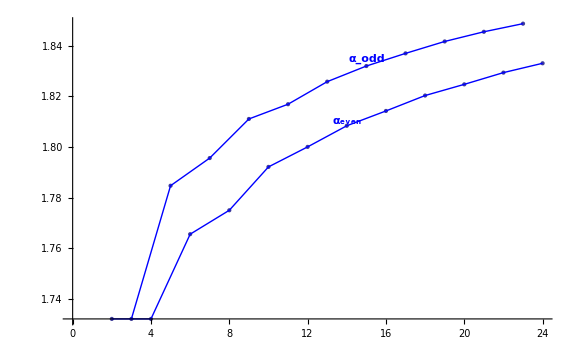

```mathematica
Table[α[n],{n,1,Ntuple}]//N
Show[
ListPlot[Table[{i,α[i]},{i,2,Ntuple}],Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],
ListPlot[Table[{i,α[i]},{i,2,Ntuple,2}],Joined->True,PlotStyle->{Blue}],ListPlot[Table[{i,α[i]},{i,3,Ntuple,2}],Joined->True,PlotStyle->{Blue}],
Graphics[{Blue,Text[Style[HoldForm[Subscript[α, even]],Large,Bold],{14,.002+α[14]}]}],
Graphics[{Blue,Text[Style[HoldForm[Subscript[α, odd]],Large,Bold],{15,.003+α[15]}]}]
]
```

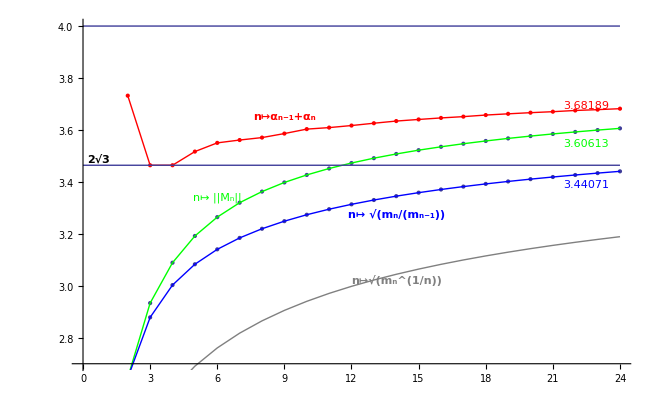

```mathematica
ma[0]=1;
Table[ma[i]=m⟦i⟧,{i,1,Length[m]}];
Show[
ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotRange->{2.7,4}],
ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Joined->True,PlotStyle->{Green}],
Graphics[{Green,Text[Style[HoldForm["n↦ ||M_n||"],Large],{6,.08+Mnorm[6]}]}],
Graphics[{Green,Text[Style[Mnorm[Ntuple],Large],{Ntuple-1.5,-.055+Mnorm[Ntuple]}]}],
Graphics[{Red,Text[Style[N[α[Ntuple-1]+α[Ntuple]],Large],{Ntuple-1.5,.015+α[Ntuple-1]+α[Ntuple]}]}],
Graphics[{Blue,Text[Style[N[(ma[Ntuple]/ma[Ntuple-1])^(1/2)],Large],{Ntuple-1.5,-.05+(ma[Ntuple]/ma[Ntuple-1])^(1/2)}]}],
Plot[8,{x,0,Ntuple}],
ListPlot[Table[{i,(ma[i]/ma[i-1])^(1/2)},{i,1,Ntuple}],Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],
ListPlot[Table[{i,(ma[i]/ma[i-1])^(1/2)},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Blue}],
Graphics[{Blue,Text[Style[HoldForm[n↦(Subscript[m, n]/Subscript[m, n-1])^(1/2)],Large,Bold],{14,-.065+(ma[14]/ma[13])^(1/2)}]}],
ListPlot[Table[{i,α[i-1]+α[i]},{i,1,Ntuple}],PlotStyle->{Red},Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],
ListPlot[Table[{i,α[i-1]+α[i]},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Red}],
Graphics[{Red,Text[Style[HoldForm[n↦Subscript[α, n-1]+Subscript[α, n]],Large,Bold],{10-1,.05+α[9]+α[10]}]}],
ListPlot[Table[{i,(ma[i]^(1/i))^(1/2)},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Gray}],
Graphics[{Gray,Text[Style[HoldForm[n↦√((Subscript[m, n])^(1/n))],Large,Bold],{14,-.02+(ma[14]^(1/(2 14)))}]}],
Graphics[{Black,Text[Style[HoldForm["2√3"],Medium,Bold],{.7,2 Sqrt[3]+.025}]}],
Plot[Sqrt[12],{x,0,Ntuple}],
Plot[4,{x,0,Ntuple}]

]
```

```mathematica
Grid[Transpose[
{Range[Length[η]],
N[Table[(ma[i]^(1/i))^(1/2),{i,1,Ntuple,1}],6],
N[Table[(ma[i]/ma[i-1])^(1/2),{i,1,Ntuple}],6],
N[Table[α[n],{n,1,Ntuple}],6],
N[Table[Mnorm[i],{i,1,Ntuple}],6],
N[Table[α[i-1]+α[i],{i,1,Ntuple}],6]}
],Alignment->Left]
```

1 | 2. | 2. | 2. | 2. | 2.+α[0]
2 | 2.30033 | 2.64575 | 1.73205 | 2.64575 | 3.73205
3 | 2.47884 | 2.87849 | 1.73205 | 2.93352 | 3.4641
4 | 2.60058 | 3.00287 | 1.73205 | 3.08891 | 3.4641
5 | 2.69061 | 3.08298 | 1.78471 | 3.19184 | 3.51676
6 | 2.76083 | 3.14038 | 1.76554 | 3.26439 | 3.55025
7 | 2.81769 | 3.18437 | 1.79564 | 3.32 | 3.56119
8 | 2.86506 | 3.21963 | 1.775 | 3.36276 | 3.57064
9 | 2.90535 | 3.24883 | 1.8111 | 3.3979 | 3.5861
10 | 2.94023 | 3.27358 | 1.79214 | 3.42682 | 3.60324
11 | 2.97083 | 3.29495 | 1.81693 | 3.45164 | 3.60907
12 | 2.998 | 3.31368 | 1.80006 | 3.47272 | 3.61699
13 | 3.02234 | 3.33028 | 1.82585 | 3.49133 | 3.62591
14 | 3.04432 | 3.34515 | 1.80841 | 3.50755 | 3.63425
15 | 3.06433 | 3.35858 | 1.83203 | 3.52217 | 3.64043
16 | 3.08264 | 3.3708 | 1.81426 | 3.53513 | 3.64629
17 | 3.09949 | 3.38198 | 1.83702 | 3.54697 | 3.65129
18 | 3.11507 | 3.39228 | 1.82036 | 3.55761 | 3.65739
19 | 3.12954 | 3.4018 | 1.84173 | 3.56745 | 3.6621
20 | 3.14303 | 3.41065 | 1.82478 | 3.57639 | 3.66651
21 | 3.15565 | 3.4189 | 1.84556 | 3.58471 | 3.67034
22 | 3.16749 | 3.42663 | 1.82942 | 3.59235 | 3.67498
23 | 3.17863 | 3.43388 | 1.84878 | 3.59952 | 3.6782
24 | 3.18914 | 3.44071 | 1.83311 | 3.60613 | 3.68189

Function[x,(2 √(12-x^2))/(π (16-x^2))]

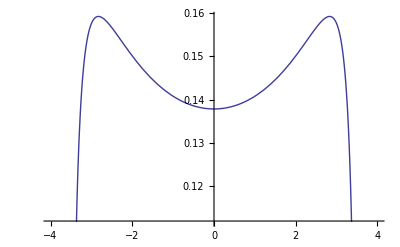

Function[n,Module[{coeffs,mlist},If[Mod[n,2]==0&&n≤2 Ntuple,coeffs=CoefficientList[LegendreP[n,x/(q+1)],x];coeffs=coeffs⟦Range[1,Length[coeffs],2]⟧;mlist=Table[ma[i],{i,0,n/2}];√((2 n+1)/(2 (q+1))) coeffs.mlist,0]]]

Function[n,√((2 n+1)/(2 (q+1))) LegendreP[n,x/(q+1)]]

```mathematica
ρFree=Function[x,2/π(√(12-x^2))/(16-x^2)]
(*Integrate[ρFree[x],{x,-√12,√12}]==1*)
Plot[ρFree[x],{x,-(q+1),(q+1)}]
ρLebesgueCoords=Function[n,Module[{coeffs,mlist},
If[Mod[n,2]==0 &&n≤2Ntuple,
coeffs=CoefficientList[LegendreP[n,x/(q+1)],x];
coeffs=coeffs⟦Range[1,Length[coeffs],2]⟧;
mlist=Table[ma[i],{i,0,n/2}];
√((2n+1)/(2(q+1)))coeffs.mlist,0]]]
p=Function[n,√((2 n+1)/(2(q+1))) LegendreP[n,x/(q+1)]]
ρLebesgue=Total[Table[ρLebesgueCoords[i]p[i],{i,0,2Ntuple}]];
ρLebesgueNminus1=Total[Table[ρLebesgueCoords[i]p[i],{i,0,2(Ntuple-1)}]];
ρLebesgueGraph=Table[{x,ρLebesgue},{x,0,q+1,1/100}];
ρLebesgueGraphTail=Table[{x,ρLebesgue},{x,34/10,q+1,1/1000}];
ρLebesgueGraphTailNminus1=Table[{x,ρLebesgueNminus1},{x,34/10,q+1,1/1000}];
```

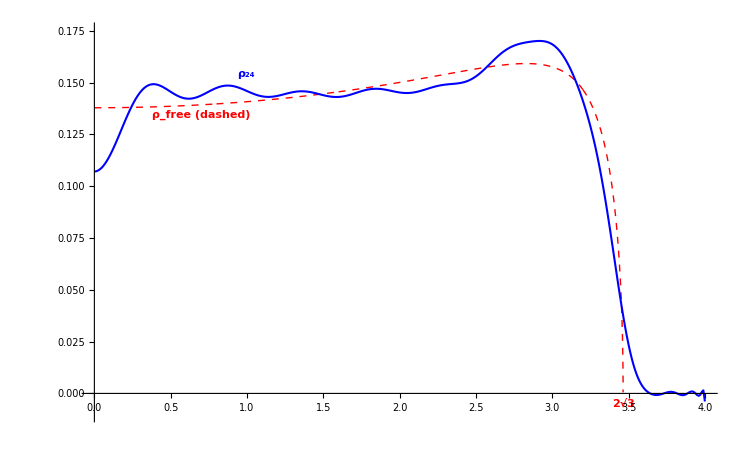

```mathematica
Show[
ListPlot[Table[{x,ρFree[x]},{x,0,q+1-1/100,1/10000}],Joined->True,PlotStyle->{Dashed,Red},PlotRange->{{0,q+1},{-.01,.175}},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],ListPlot[ρLebesgueGraph,Joined->True,PlotStyle->{Directive[Blue,Thickness[.002]]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,Thickness[.002]]}],
Graphics[{Blue,Text[Style[HoldForm[Subscript[ρ, 24]],Large,Bold],Evaluate[ρLebesgueGraph⟦100⟧+{0,.008}]]}],
Graphics[{Red,Text[Style[HoldForm[Subscript[ρ, free]"(dashed)"],Large,Bold],Evaluate[{0.7,ρFree[0.7]-.005}]]}],Graphics[{Red,Text[Style[HoldForm["2√3"],Medium,Bold],{2Sqrt[3],-0.005}]}]
]
```

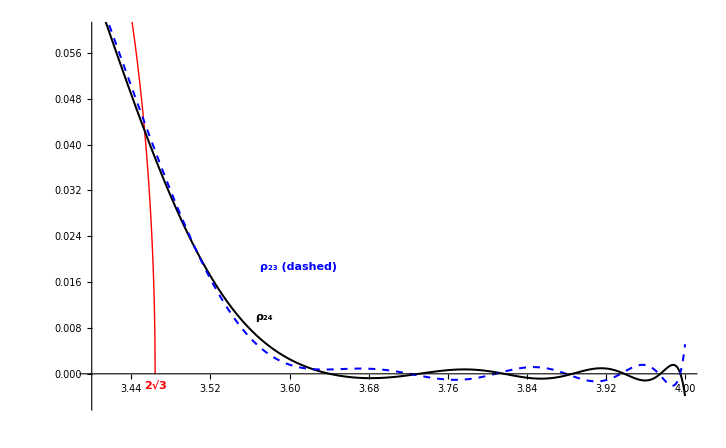

```mathematica
Show[ListPlot[Join[Table[{x,ρFree[x]},{x,3.4,2Sqrt[3],1/10000}],{{2Sqrt[3],0}}],Joined->True,PlotStyle->{Red},PlotRange->{{3.4,q+1},{-.005,.06}},AxesOrigin->{3.4,0},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotRange->{2.7,4}],
ListPlot[ρLebesgueGraphTail,Joined->True,PlotStyle->{Directive[Black,Thickness[.002]]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,Thickness[.002]]}],
Graphics[{Black,Text[Style[HoldForm[Subscript[ρ, 24]],Large,Bold],Evaluate[ρLebesgueGraphTail⟦150⟧+{.025,.00}]]}],
ListPlot[ρLebesgueGraphTailNminus1,Joined->True,PlotStyle->{Directive[Dashed,Blue,Thickness[.002]]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,Thickness[.002]]}],
Graphics[{Blue,Text[Style[HoldForm[Subscript[ρ, 23]"(dashed)"],Large,Bold],Evaluate[ρLebesgueGraphTailNminus1⟦150⟧+{0.06,0.01}]]}],
Graphics[{Red,Text[Style[HoldForm["2√3"],Medium,Bold],{2Sqrt[3],-0.002}]}]]
```

```mathematica
(ρLebesgueGraphTail+ρLebesgueGraphTailNminus1)/2//N//ColumnForm
```

{3.4,0.0688256}
{3.401,0.0683415}
{3.402,0.067857}
{3.403,0.0673722}
{3.404,0.066887}
{3.405,0.0664014}
{3.406,0.0659156}
{3.407,0.0654295}
{3.408,0.0649432}
{3.409,0.0644567}
{3.41,0.06397}
{3.411,0.0634832}
{3.412,0.0629963}
{3.413,0.0625092}
{3.414,0.0620221}
{3.415,0.061535}
{3.416,0.0610479}
{3.417,0.0605609}
{3.418,0.0600739}
{3.419,0.0595869}
{3.42,0.0591002}
{3.421,0.0586136}
{3.422,0.0581271}
{3.423,0.0576409}
{3.424,0.057155}
{3.425,0.0566693}
{3.426,0.056184}
{3.427,0.055699}
{3.428,0.0552145}
{3.429,0.0547303}
{3.43,0.0542466}
{3.431,0.0537634}
{3.432,0.0532807}
{3.433,0.0527985}
{3.434,0.052317}
{3.435,0.0518361}
{3.436,0.0513558}
{3.437,0.0508762}
{3.438,0.0503974}
{3.439,0.0499193}
{3.44,0.049442}
{3.441,0.0489656}
{3.442,0.04849}
{3.443,0.0480153}
{3.444,0.0475415}
{3.445,0.0470688}
{3.446,0.046597}
{3.447,0.0461263}
{3.448,0.0456566}
{3.449,0.0451881}
{3.45,0.0447207}
{3.451,0.0442545}
{3.452,0.0437896}
{3.453,0.0433258}
{3.454,0.0428634}
{3.455,0.0424023}
{3.456,0.0419425}
{3.457,0.0414842}
{3.458,0.0410273}
{3.459,0.0405718}
{3.46,0.0401178}
{3.461,0.0396654}
{3.462,0.0392146}
{3.463,0.0387653}
{3.464,0.0383177}
{3.465,0.0378717}
{3.466,0.0374275}
{3.467,0.036985}
{3.468,0.0365443}
{3.469,0.0361054}
{3.47,0.0356683}
{3.471,0.0352331}
{3.472,0.0347998}
{3.473,0.0343685}
{3.474,0.0339391}
{3.475,0.0335118}
{3.476,0.0330864}
{3.477,0.0326632}
{3.478,0.032242}
{3.479,0.031823}
{3.48,0.0314062}
{3.481,0.0309915}
{3.482,0.0305791}
{3.483,0.0301689}
{3.484,0.0297611}
{3.485,0.0293555}
{3.486,0.0289523}
{3.487,0.0285514}
{3.488,0.028153}
{3.489,0.027757}
{3.49,0.0273635}
{3.491,0.0269724}
{3.492,0.0265839}
{3.493,0.0261979}
{3.494,0.0258145}
{3.495,0.0254336}
{3.496,0.0250554}
{3.497,0.0246799}
{3.498,0.024307}
{3.499,0.0239368}
{3.5,0.0235693}
{3.501,0.0232045}
{3.502,0.0228426}
{3.503,0.0224834}
{3.504,0.022127}
{3.505,0.0217734}
{3.506,0.0214227}
{3.507,0.0210749}
{3.508,0.02073}
{3.509,0.0203879}
{3.51,0.0200488}
{3.511,0.0197127}
{3.512,0.0193795}
{3.513,0.0190493}
{3.514,0.018722}
{3.515,0.0183978}
{3.516,0.0180767}
{3.517,0.0177585}
{3.518,0.0174435}
{3.519,0.0171315}
{3.52,0.0168225}
{3.521,0.0165167}
{3.522,0.016214}
{3.523,0.0159144}
{3.524,0.0156179}
{3.525,0.0153246}
{3.526,0.0150344}
{3.527,0.0147474}
{3.528,0.0144635}
{3.529,0.0141829}
{3.53,0.0139054}
{3.531,0.013631}
{3.532,0.0133599}
{3.533,0.013092}
{3.534,0.0128272}
{3.535,0.0125657}
{3.536,0.0123074}
{3.537,0.0120523}
{3.538,0.0118003}
{3.539,0.0115516}
{3.54,0.0113062}
{3.541,0.0110639}
{3.542,0.0108248}
{3.543,0.0105889}
{3.544,0.0103563}
{3.545,0.0101268}
{3.546,0.00990054}
{3.547,0.00967747}
{3.548,0.00945758}
{3.549,0.00924087}
{3.55,0.00902734}
{3.551,0.00881697}
{3.552,0.00860977}
{3.553,0.00840571}
{3.554,0.0082048}
{3.555,0.00800702}
{3.556,0.00781236}
{3.557,0.00762081}
{3.558,0.00743235}
{3.559,0.00724699}
{3.56,0.0070647}
{3.561,0.00688546}
{3.562,0.00670928}
{3.563,0.00653612}
{3.564,0.00636598}
{3.565,0.00619884}
{3.566,0.00603468}
{3.567,0.00587349}
{3.568,0.00571525}
{3.569,0.00555993}
{3.57,0.00540752}
{3.571,0.00525801}
{3.572,0.00511137}
{3.573,0.00496758}
{3.574,0.00482661}
{3.575,0.00468846}
{3.576,0.00455309}
{3.577,0.00442048}
{3.578,0.00429062}
{3.579,0.00416346}
{3.58,0.00403901}
{3.581,0.00391722}
{3.582,0.00379807}
{3.583,0.00368154}
{3.584,0.00356759}
{3.585,0.00345622}
{3.586,0.00334738}
{3.587,0.00324105}
{3.588,0.00313721}
{3.589,0.00303582}
{3.59,0.00293686}
{3.591,0.00284029}
{3.592,0.0027461}
{3.593,0.00265424}
{3.594,0.0025647}
{3.595,0.00247743}
{3.596,0.00239242}
{3.597,0.00230962}
{3.598,0.00222901}
{3.599,0.00215056}
{3.6,0.00207423}
{3.601,0.002}
{3.602,0.00192783}
{3.603,0.0018577}
{3.604,0.00178956}
{3.605,0.00172338}
{3.606,0.00165914}
{3.607,0.0015968}
{3.608,0.00153633}
{3.609,0.00147769}
{3.61,0.00142085}
{3.611,0.00136579}
{3.612,0.00131246}
{3.613,0.00126083}
{3.614,0.00121087}
{3.615,0.00116254}
{3.616,0.00111582}
{3.617,0.00107067}
{3.618,0.00102705}
{3.619,0.000984938}
{3.62,0.000944294}
{3.621,0.000905085}
{3.622,0.000867279}
{3.623,0.000830844}
{3.624,0.000795746}
{3.625,0.000761951}
{3.626,0.000729429}
{3.627,0.000698145}
{3.628,0.000668069}
{3.629,0.000639167}
{3.63,0.000611407}
{3.631,0.000584758}
{3.632,0.000559189}
{3.633,0.000534667}
{3.634,0.000511162}
{3.635,0.000488642}
{3.636,0.000467078}
{3.637,0.000446439}
{3.638,0.000426695}
{3.639,0.000407816}
{3.64,0.000389772}
{3.641,0.000372536}
{3.642,0.000356077}
{3.643,0.000340369}
{3.644,0.000325382}
{3.645,0.000311089}
{3.646,0.000297462}
{3.647,0.000284476}
{3.648,0.000272104}
{3.649,0.000260319}
{3.65,0.000249096}
{3.651,0.00023841}
{3.652,0.000228237}
{3.653,0.000218551}
{3.654,0.00020933}
{3.655,0.00020055}
{3.656,0.000192188}
{3.657,0.000184222}
{3.658,0.000176631}
{3.659,0.000169392}
{3.66,0.000162485}
{3.661,0.00015589}
{3.662,0.000149588}
{3.663,0.000143558}
{3.664,0.000137782}
{3.665,0.000132243}
{3.666,0.000126922}
{3.667,0.000121802}
{3.668,0.000116868}
{3.669,0.000112103}
{3.67,0.000107491}
{3.671,0.000103019}
{3.672,0.0000986706}
{3.673,0.0000944337}
{3.674,0.0000902947}
{3.675,0.000086241}
{3.676,0.0000822607}
{3.677,0.0000783424}
{3.678,0.0000744752}
{3.679,0.0000706488}
{3.68,0.0000668535}
{3.681,0.0000630801}
{3.682,0.0000593201}
{3.683,0.0000555654}
{3.684,0.0000518085}
{3.685,0.0000480425}
{3.686,0.0000442609}
{3.687,0.0000404579}
{3.688,0.0000366281}
{3.689,0.0000327669}
{3.69,0.0000288698}
{3.691,0.0000249332}
{3.692,0.0000209538}
{3.693,0.0000169289}
{3.694,0.0000128561}
{3.695,8.73381×10^-6}
{3.696,4.56069×10^-6}
{3.697,3.35928×10^-7}
{3.698,-3.94082×10^-6}
{3.699,-8.26944×10^-6}
{3.7,-0.0000126494}
{3.701,-0.0000170797}
{3.702,-0.000021559}
{3.703,-0.0000260855}
{3.704,-0.0000306569}
{3.705,-0.0000352706}
{3.706,-0.0000399238}
{3.707,-0.000044613}
{3.708,-0.0000493347}
{3.709,-0.0000540847}
{3.71,-0.0000588588}
{3.711,-0.0000636523}
{3.712,-0.0000684603}
{3.713,-0.0000732776}
{3.714,-0.0000780987}
{3.715,-0.0000829179}
{3.716,-0.0000877291}
{3.717,-0.0000925263}
{3.718,-0.0000973031}
{3.719,-0.000102053}
{3.72,-0.000106769}
{3.721,-0.000111444}
{3.722,-0.000116071}
{3.723,-0.000120644}
{3.724,-0.000125154}
{3.725,-0.000129595}
{3.726,-0.000133958}
{3.727,-0.000138237}
{3.728,-0.000142424}
{3.729,-0.000146511}
{3.73,-0.000150491}
{3.731,-0.000154356}
{3.732,-0.000158099}
{3.733,-0.000161711}
{3.734,-0.000165186}
{3.735,-0.000168516}
{3.736,-0.000171694}
{3.737,-0.000174713}
{3.738,-0.000177566}
{3.739,-0.000180244}
{3.74,-0.000182743}
{3.741,-0.000185055}
{3.742,-0.000187174}
{3.743,-0.000189094}
{3.744,-0.000190808}
{3.745,-0.000192311}
{3.746,-0.000193597}
{3.747,-0.000194661}
{3.748,-0.000195498}
{3.749,-0.000196103}
{3.75,-0.000196472}
{3.751,-0.0001966}
{3.752,-0.000196485}
{3.753,-0.000196121}
{3.754,-0.000195507}
{3.755,-0.00019464}
{3.756,-0.000193516}
{3.757,-0.000192135}
{3.758,-0.000190494}
{3.759,-0.000188592}
{3.76,-0.000186428}
{3.761,-0.000184002}
{3.762,-0.000181315}
{3.763,-0.000178365}
{3.764,-0.000175154}
{3.765,-0.000171684}
{3.766,-0.000167956}
{3.767,-0.000163972}
{3.768,-0.000159735}
{3.769,-0.000155247}
{3.77,-0.000150513}
{3.771,-0.000145536}
{3.772,-0.000140321}
{3.773,-0.000134872}
{3.774,-0.000129195}
{3.775,-0.000123295}
{3.776,-0.000117179}
{3.777,-0.000110853}
{3.778,-0.000104325}
{3.779,-0.0000976016}
{3.78,-0.0000906908}
{3.781,-0.0000836011}
{3.782,-0.0000763412}
{3.783,-0.0000689202}
{3.784,-0.0000613477}
{3.785,-0.0000536337}
{3.786,-0.0000457884}
{3.787,-0.0000378224}
{3.788,-0.0000297468}
{3.789,-0.000021573}
{3.79,-0.0000133126}
{3.791,-4.97751×10^-6}
{3.792,3.41989×10^-6}
{3.793,0.0000118671}
{3.794,0.0000203513}
{3.795,0.0000288594}
{3.796,0.0000373782}
{3.797,0.0000458942}
{3.798,0.0000543937}
{3.799,0.0000628629}
{3.8,0.0000712878}
{3.801,0.0000796544}
{3.802,0.0000879483}
{3.803,0.0000961555}
{3.804,0.000104261}
{3.805,0.000112252}
{3.806,0.000120112}
{3.807,0.000127829}
{3.808,0.000135387}
{3.809,0.000142772}
{3.81,0.00014997}
{3.811,0.000156967}
{3.812,0.00016375}
{3.813,0.000170304}
{3.814,0.000176617}
{3.815,0.000182674}
{3.816,0.000188463}
{3.817,0.000193972}
{3.818,0.000199187}
{3.819,0.000204098}
{3.82,0.000208691}
{3.821,0.000212956}
{3.822,0.000216883}
{3.823,0.000220461}
{3.824,0.000223679}
{3.825,0.000226529}
{3.826,0.000229001}
{3.827,0.000231088}
{3.828,0.000232782}
{3.829,0.000234075}
{3.83,0.000234962}
{3.831,0.000235436}
{3.832,0.000235492}
{3.833,0.000235127}
{3.834,0.000234336}
{3.835,0.000233116}
{3.836,0.000231466}
{3.837,0.000229383}
{3.838,0.000226869}
{3.839,0.000223922}
{3.84,0.000220544}
{3.841,0.000216737}
{3.842,0.000212505}
{3.843,0.000207849}
{3.844,0.000202777}
{3.845,0.000197292}
{3.846,0.000191401}
{3.847,0.000185112}
{3.848,0.000178434}
{3.849,0.000171374}
{3.85,0.000163944}
{3.851,0.000156155}
{3.852,0.000148018}
{3.853,0.000139546}
{3.854,0.000130754}
{3.855,0.000121655}
{3.856,0.000112266}
{3.857,0.000102603}
{3.858,0.0000926833}
{3.859,0.0000825249}
{3.86,0.0000721468}
{3.861,0.0000615689}
{3.862,0.0000508116}
{3.863,0.0000398963}
{3.864,0.000028845}
{3.865,0.0000176802}
{3.866,6.42543×10^-6}
{3.867,-4.89548×10^-6}
{3.868,-0.000016258}
{3.869,-0.0000276371}
{3.87,-0.0000390072}
{3.871,-0.0000503424}
{3.872,-0.0000616164}
{3.873,-0.0000728023}
{3.874,-0.0000838732}
{3.875,-0.000094802}
{3.876,-0.000105561}
{3.877,-0.000116123}
{3.878,-0.000126461}
{3.879,-0.000136546}
{3.88,-0.000146351}
{3.881,-0.00015585}
{3.882,-0.000165015}
{3.883,-0.000173818}
{3.884,-0.000182235}
{3.885,-0.000190238}
{3.886,-0.000197802}
{3.887,-0.000204903}
{3.888,-0.000211516}
{3.889,-0.000217618}
{3.89,-0.000223186}
{3.891,-0.000228198}
{3.892,-0.000232635}
{3.893,-0.000236475}
{3.894,-0.000239702}
{3.895,-0.000242298}
{3.896,-0.000244246}
{3.897,-0.000245534}
{3.898,-0.000246147}
{3.899,-0.000246075}
{3.9,-0.000245308}
{3.901,-0.000243838}
{3.902,-0.00024166}
{3.903,-0.000238769}
{3.904,-0.000235163}
{3.905,-0.000230842}
{3.906,-0.000225809}
{3.907,-0.000220067}
{3.908,-0.000213624}
{3.909,-0.000206487}
{3.91,-0.000198668}
{3.911,-0.000190181}
{3.912,-0.000181042}
{3.913,-0.000171269}
{3.914,-0.000160884}
{3.915,-0.00014991}
{3.916,-0.000138373}
{3.917,-0.000126302}
{3.918,-0.000113728}
{3.919,-0.000100685}
{3.92,-0.0000872103}
{3.921,-0.0000733422}
{3.922,-0.0000591224}
{3.923,-0.0000445948}
{3.924,-0.000029806}
{3.925,-0.0000148046}
{3.926,3.58115×10^-7}
{3.927,0.000015629}
{3.928,0.0000309527}
{3.929,0.0000462717}
{3.93,0.0000615269}
{3.931,0.0000766573}
{3.932,0.0000916004}
{3.933,0.000106292}
{3.934,0.000120668}
{3.935,0.00013466}
{3.936,0.000148203}
{3.937,0.000161229}
{3.938,0.000173669}
{3.939,0.000185456}
{3.94,0.000196522}
{3.941,0.000206799}
{3.942,0.000216222}
{3.943,0.000224724}
{3.944,0.000232242}
{3.945,0.000238713}
{3.946,0.000244079}
{3.947,0.000248283}
{3.948,0.00025127}
{3.949,0.00025299}
{3.95,0.000253397}
{3.951,0.000252449}
{3.952,0.00025011}
{3.953,0.000246348}
{3.954,0.000241139}
{3.955,0.000234465}
{3.956,0.000226313}
{3.957,0.000216682}
{3.958,0.000205577}
{3.959,0.000193011}
{3.96,0.000179009}
{3.961,0.000163606}
{3.962,0.000146847}
{3.963,0.000128789}
{3.964,0.000109503}
{3.965,0.0000890718}
{3.966,0.0000675914}
{3.967,0.0000451736}
{3.968,0.000021945}
{3.969,-1.95179×10^-6}
{3.97,-0.0000263574}
{3.971,-0.0000510951}
{3.972,-0.0000759701}
{3.973,-0.000100769}
{3.974,-0.000125258}
{3.975,-0.000149185}
{3.976,-0.000172275}
{3.977,-0.000194234}
{3.978,-0.000214744}
{3.979,-0.000233466}
{3.98,-0.000250037}
{3.981,-0.000264071}
{3.982,-0.000275159}
{3.983,-0.000282866}
{3.984,-0.000286734}
{3.985,-0.000286281}
{3.986,-0.000280998}
{3.987,-0.000270354}
{3.988,-0.000253792}
{3.989,-0.000230729}
{3.99,-0.000200559}
{3.991,-0.000162654}
{3.992,-0.00011636}
{3.993,-0.0000610017}
{3.994,4.11863×10^-6}
{3.995,0.0000797188}
{3.996,0.000166536}
{3.997,0.000265327}
{3.998,0.000376863}
{3.999,0.000501931}
{4.,0.000641329}

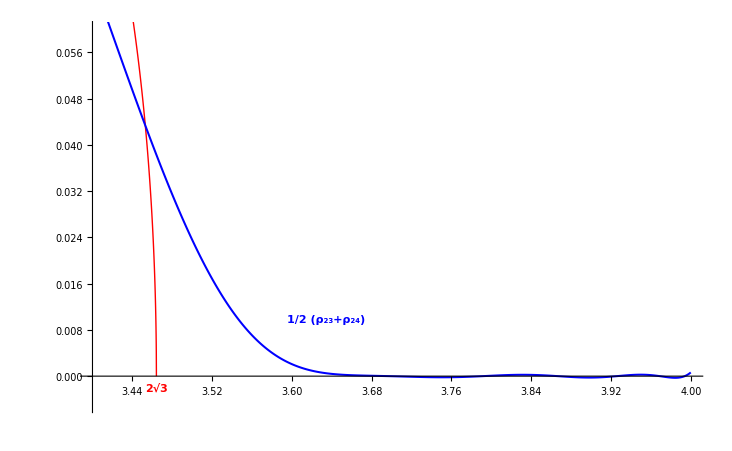

```mathematica
Show[ListPlot[Join[Table[{x,ρFree[x]},{x,3.4,2Sqrt[3],1/10000}],{{2Sqrt[3],0}}],Joined->True,PlotStyle->{Red},PlotRange->{{3.4,q+1},{-.005,.06}},AxesOrigin->{3.4,0},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotRange->{2.7,4}],
ListPlot[(ρLebesgueGraphTail+ρLebesgueGraphTailNminus1)/2,Joined->True,PlotStyle->{Directive[Blue,Thickness[.002]]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,Thickness[.002]]}],
Graphics[{Blue,Text[Style[HoldForm[1/2(Subscript[ρ, 23]+Subscript[ρ, 24])],Large,Bold],Evaluate[ρLebesgueGraphTail⟦150⟧+{.085,.00}]]}],
Graphics[{Red,Text[Style[HoldForm["2√3"],Medium,Bold],{2Sqrt[3],-0.002}]}]]
```